{a→0.157044}

NonlinearModelFit::fitc: Number of coordinates (2) is not equal to the number of variables (1).

NonlinearModelFit[{{2.4,0.425,0.935},{3.5,0.385,1.26},{1.9,0.465,0.81},{1.2,0.56,0.6}},a Cos[θ]^2,{a},θ]

NonlinearModelFit::fitc: Number of coordinates (2) is not equal to the number of variables (1).

NonlinearModelFit[{{2.4,0.425,0.935},{3.5,0.385,1.26},{1.9,0.465,0.81},{1.2,0.56,0.6}},a Cos[θ]^2,{a},θ][ParameterTable]

ListPlot::lpn: RelAngIntData is not a list of numbers or pairs of numbers.

Show::gcomb: Could not combine the graphics objects in Show[,ListPlot[RelAngIntData],AxesLabel→{θ (Rad),intensity (%)}].

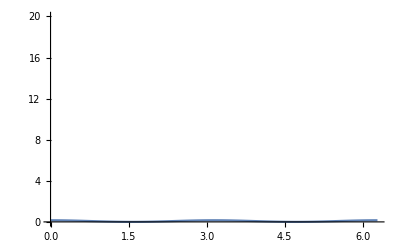
Show[-Graphics-,ListPlot[RelAngIntData],AxesLabel→{θ (Rad),intensity (%)}]

```mathematica
Clear[x, y, z];

MagFocData = {{2.4,0.425, 0.935},{3.5,0.385, 1.260},{1.9,0.465, 0.810},{1.2,0.560, 0.600}};

FindFit[MagFocData,a ((y / z) - x),{a}, {x,y,z}]

intensity[θ_]=a (Cos[θ])^2/.%;

nlm=NonlinearModelFit[MagFocData,a (Cos[θ])^2,{a},θ];
Normal[nlm]
nlm["ParameterTable"]

Show[Plot[intensity[θ],{θ,0,2 Pi},PlotRange->{0,20}],ListPlot[RelAngIntData],AxesLabel->{"θ (Rad)","intensity (%)"}]
```